## Проверка на симметричность ядра

```mathematica
kernel[t_,s_]:=Piecewise[{{-t,0<=t<=s},{-s,s<=t≤1}}]
```

```mathematica
kernel[t,s]
```

Piecewise[{{-t, 0≤t≤s}, {-s, s≤t≤1}, {0, True}}]

```mathematica
Plot3D[kernel[t,s],{t,0,1},{s,0,1}]
```

-Graphics3D-

```mathematica
kernel[s,t]
```

Piecewise[{{-s, 0≤s≤t}, {-t, t≤s≤1}, {0, True}}]

```mathematica
Plot3D[kernel[s,t],{t,0,1},{s,0,1}]
```

-Graphics3D-

## Сведение ИУ к задаче Ш-Л

```mathematica
D[λ∫_0^t -s x[s]ⅆs+λ∫_t^1 -t* x[s]ⅆs, t]
```

-t λ x[t]+λ (∫_t^1 -x[s]ⅆs+t x[t])

```mathematica
D[-t λ x[t]+λ (∫_t^1 -x[s]ⅆs+t x[t]), t]//FullSimplify
```

λ x[t]

```mathematica
-t λ x[t]+λ (∫_t^1 -x[s]ⅆs+t x[t])//.{t->1}
```

0

```mathematica
λ∫_0^t -s x[s]ⅆs+λ∫_t^1 -t* x[s]ⅆs//.{t->0}
```

0

## Решение задачи Ш-Л

```mathematica
DSolve[{x''[t]-λ*x[t]==0, x[0]==0, x'[1]==0},x[t],t]
```

{{x[t]→Piecewise[{{C[1] Sin[t √-λ], n∈ℤ&&n≥1&&-λ==(-1/2+n)^2 π^2}, {0, True}}]}}

## Ортонормирование системы собственных функций

```mathematica
Solve[C[1]^2∫_0^1 Sin[t √((-1/2+n)^2 π^2)]^2 ⅆt==1,C[1]]//FullSimplify
```

{{C[1]→-(√(2 π))/(√(π+Sin[2 n π]/(-1+2 n)))},{C[1]→(√(2 π))/(√(π+Sin[2 n π]/(-1+2 n)))}}

```mathematica
∫_0^1 2*Sin[t √((-1/2+n)^2 π^2)]^2 ⅆt//FullSimplify
```

1-Sin[2 n π]/(π-2 n π)

## Построение повторных ядер

```mathematica
K[n_]:=∑_(k=1)^∞ (2*Sin[t (-1/2+k) π]*Sin[s (-1/2+k) π])/((-(-1/2+k)^2 π^2)^n)
```

```mathematica
K[2]
```

1/(2 π^4)ⅇ^(-1/2 ⅈ π s-ⅈ π (s-t)-(ⅈ π t)/2-ⅈ π (s+t)) (ⅇ^(ⅈ π s+ⅈ π (s+t)) LerchPhi[ⅇ^(-ⅈ π (s-t)),4,1/2]+ⅇ^(2 ⅈ π (s-t)+ⅈ π t+ⅈ π (s+t)) LerchPhi[ⅇ^(ⅈ π (s-t)),4,1/2]-ⅇ^(ⅈ π s+ⅈ π (s-t)+ⅈ π t) LerchPhi[ⅇ^(-ⅈ π (s+t)),4,1/2]-ⅇ^(ⅈ π (s-t)+2 ⅈ π (s+t)) LerchPhi[ⅇ^(ⅈ π (s+t)),4,1/2])

```mathematica
Plot3D[K[2],{t, 0, 1},{s,0,1}]
```

-Graphics3D-

```mathematica
K[3]
```

-1/(2 π^6)ⅇ^(-1/2 ⅈ π s-ⅈ π (s-t)-(ⅈ π t)/2-ⅈ π (s+t)) (ⅇ^(ⅈ π s+ⅈ π (s+t)) LerchPhi[ⅇ^(-ⅈ π (s-t)),6,1/2]+ⅇ^(2 ⅈ π (s-t)+ⅈ π t+ⅈ π (s+t)) LerchPhi[ⅇ^(ⅈ π (s-t)),6,1/2]-ⅇ^(ⅈ π s+ⅈ π (s-t)+ⅈ π t) LerchPhi[ⅇ^(-ⅈ π (s+t)),6,1/2]-ⅇ^(ⅈ π (s-t)+2 ⅈ π (s+t)) LerchPhi[ⅇ^(ⅈ π (s+t)),6,1/2])

```mathematica
Plot3D[K[3],{t, 0, 1},{s,0,1}]
```

-Graphics3D-

## Разложение f(t) в ряд Фурье по ОНС

```mathematica
function[t_]:=t+1
```

```mathematica
u[k_]:=2^(1/2)Sin[t (-1/2+k) π]
```

```mathematica
f[k_]=∫_0^1 function[t]*u[k]ⅆt//FullSimplify
```

-(2 √2 (2 Cos[k π]+(-1+2 k) π (-1+2 Sin[k π])))/(π-2 k π)^2

```mathematica
f[1]
```

-(2 √2 (-2-π))/π^2

```mathematica
f[2]
```

-(2 √2 (2-3 π))/(9 π^2)

```mathematica
∑_(k=1)^∞ -(2 √2 (2 Cos[k π]+(-1+2 k) π (-1+2 Sin[k π])))/(π-2 k π)^2*2^(1/2)Sin[t (-1/2+k) π]
```

-1/π^2 ⅈ ⅇ^(-1/2 ⅈ π t) (-2 ⅇ^((ⅈ π t)/2) π ArcTanh[ⅇ^(-1/2 ⅈ π t)]+2 ⅇ^((ⅈ π t)/2) π ArcTanh[ⅇ^((ⅈ π t)/2)]-LerchPhi[-ⅇ^(-ⅈ π t),2,1/2]+ⅇ^(ⅈ π t) LerchPhi[-ⅇ^(ⅈ π t),2,1/2])

```mathematica
Sum[-(2 √2 (2 Cos[k π]+(-1+2 k) π (-1+2 Sin[k π])))/(π-2 k π)^2*2^(1/2)Sin[t (-1/2+k) π],{k,∞},GenerateConditions->True]
```

ConditionalExpression[-1/π^2 ⅈ ⅇ^(-1/2 ⅈ π t) (-2 ⅇ^((ⅈ π t)/2) π ArcTanh[ⅇ^(-1/2 ⅈ π t)]+2 ⅇ^((ⅈ π t)/2) π ArcTanh[ⅇ^((ⅈ π t)/2)]-LerchPhi[-ⅇ^(-ⅈ π t),2,1/2]+ⅇ^(ⅈ π t) LerchPhi[-ⅇ^(ⅈ π t),2,1/2]),ⅇ^(ⅈ π t)≠1&&ⅇ^(π Im[t])==1]

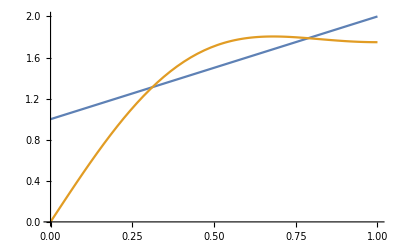

```mathematica
Plot[{function[t],∑_(k=1)^2 -(2 √2 (2 Cos[k π]+(-1+2 k) π (-1+2 Sin[k π])))/(π-2 k π)^2*2^(1/2)Sin[t (-1/2+k) π]},{t,0,1} ]
```

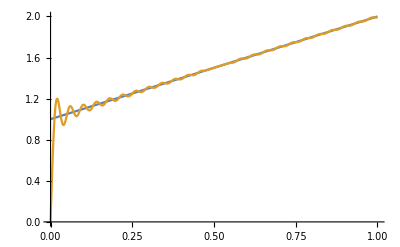

```mathematica
Plot[{function[t],∑_(k=1)^50 -(2 √2 (2 Cos[k π]+(-1+2 k) π (-1+2 Sin[k π])))/(π-2 k π)^2*2^(1/2)Sin[t (-1/2+k) π]},{t,0,1} ]
```

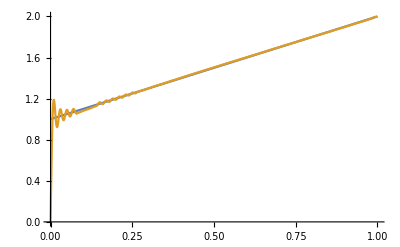

```mathematica
Plot[{function[t],∑_(k=1)^100 -(2 √2 (2 Cos[k π]+(-1+2 k) π (-1+2 Sin[k π])))/(π-2 k π)^2*2^(1/2)Sin[t (-1/2+k) π]},{t,0,1} ]
```